### Here is a long list of random 2D vectors.

```mathematica
ran2D=Table[{RandomVariate[ExponentialDistribution[1]],RandomVariate[ExponentialDistribution[1]]},{5000}]
```

{{0.023557,0.74007},{1.66145,0.297172},4996,{2.9656,0.328111},{2.17337,0.65666}}
 |  |  |  |

### Use Short ( look it up ) to view the first 10 or so elements

```mathematica
Short[ran2D,10]
```

{{0.023557,0.74007},{1.66145,0.297172},{0.509944,0.416073},{0.00712819,1.43791},{0.304951,0.47925},«4990»,{1.02895,1.8911},{3.32264,1.52919},{0.80859,0.869664},{2.9656,0.328111},{2.17337,0.65666}}

### Use Map and a pure function to construct a list of the length of these vectors.

```mathematica
mag[{x_,y_}]:=Sqrt[x^2 + y^2]
lengths=Map[mag[#]&,ran2D];

lengths2=Map[Sqrt[#.#] &,ran2D];
```

### Make a histogram of the distribution of lengths using Histogram.

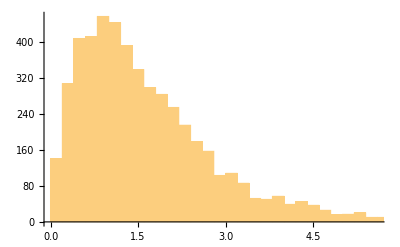

```mathematica
Histogram[lengths2]
```

### Use Select and a pure function to make a list of the vectors with length greater than 6

```mathematica
over6=Select[lengths,#>6&]
```

{6.70158,7.40842,7.36149,6.18343,6.30254,7.34533,6.18749,6.39957,6.32146,6.43557,6.07684,6.8517,8.56399,6.5239,6.95839,6.07442,7.05617,6.45945,7.42924,7.22907,6.35877,6.3715,6.78557,6.3976,7.43447,6.56753,7.7214,6.38382,6.47751,8.20894,7.56385,9.33413,6.55029,6.06046,7.48811,7.17762,6.41999}

### Here is a series

```mathematica
s1=Series[(1+z)^(1/2),{z,0,10}]
```

1+z/2-z^2/8+z^3/16-(5 z^4)/128+(7 z^5)/256-(21 z^6)/1024+(33 z^7)/2048-(429 z^8)/32768+(715 z^9)/65536-(2431 z^10)/262144+O[z]^11

### Construct a list of the numerators and another list of the denominators of each term. Look up Numerator and Denominator. Convert the expression into a list and Use Map and a pure function.

```mathematica
s1list=Apply[List,Normal[s1]]
```

{1,z/2,-z^2/8,z^3/16,-(5 z^4)/128,(7 z^5)/256,-(21 z^6)/1024,(33 z^7)/2048,-(429 z^8)/32768,(715 z^9)/65536,-(2431 z^10)/262144}

```mathematica
nums=Map[Numerator[#]&,s1list]
dems=Map[Denominator[#]&,s1list]
```

{1,z,-z^2,z^3,-5 z^4,7 z^5,-21 z^6,33 z^7,-429 z^8,715 z^9,-2431 z^10}

{1,2,8,16,128,256,1024,2048,32768,65536,262144}

### Most differential equations with non constant coefficients do not have closed form solutions. Somewhat miraculously, this one does

```mathematica
specialDE=h''''[r]+2/r h'''[r]-1/r^2 h''[r] +1/r^3 h'[r]==0
```

h'[r]/r^3-h''[r]/r^2+(2 h^(3)[r])/r+h^(4)[r]==0

### Find the general solution

```mathematica
gensol=DSolve[specialDE,h[r],r]
```

{{h[r]→(r^2 C[2])/2-(r^2 C[3])/4+C[4]+C[1] Log[r]+1/2 r^2 C[3] Log[r]}}

### Then find the special solution that satisfies the boundary conditions h[0]=1, h’[0]=0 , h[10]=0, h’[10]=0

```mathematica
specsol=DSolveValue[{specialDE,h[0]==1,h'[0]==0,h[10]==0,h'[10]==0},h[r],r]
```

1/100 (100-r^2-2 r^2 Log[10]+2 r^2 Log[r])

### Finally, make sure that your solution works by plugging back into the DE using Function. If you use an expression inside Function, be sure to use Evaluate.

```mathematica
specialDE /.h-> Function[r,specsol] (*this line is trash and whatever you write instead of specsol it will always be true*)
```

True

```mathematica
specialDE /.h-> Function[r,Evaluate[specsol]]
```

1/(25 r^2)-(4-4 Log[10]+4 Log[r])/(100 r^2)+(-4 r Log[10]+4 r Log[r])/(100 r^3)==0

```mathematica
Simplify[%]
```

True